## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
SetOptions[EvaluationNotebook[],OutputSizeLimit->100]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Data
 |  |  |  |

## Function Definitions

### General Data Manipulation

```mathematica
ClearAll[select,where];
SetAttributes[where,HoldAll];
select[table:{colNames_List,rows__List},w:(where[condition_]|None):None,cols:(columns[varNames__]|All):All]:=With[{namingRules=Dispatch[Thread[colNames->Thread[Slot[Range[Length[colNames]]]]]]},With[{cl={varNames}/.namingRules/.Verbatim[Slot][n_]:>n},If[cols===All,#,#[[All,cl]]]&@If[w===None,{rows},(*else*)With[{selF=Apply[Function,Hold[condition]/.namingRules]},Select[{rows},selF@@#&]]]]];
```

### Manipulation of Proof Compression Data

```mathematica
TotalCompressionRatio[original_,compressed_]:= ((Total[original]-Total[compressed])/Total[original]);
CompressionRatios[original_,compressed_] := Inner[(#1  -#2 )/#1&, original, compressed,List];
CompressionProportion[original_,compressed_]:=With[{data = Transpose[{original,compressed}]},Length[Select[data, #[[2]]< #[[1]] & ]]/Length[data] ];
```

```mathematica
FilterCompressed[original_,compressed_]:=With[{data = Transpose[{original,compressed}]},Transpose[Select[data, #[[2]]< #[[1]] & ]]];
```

## Data Loading

```mathematica
header = {"GoalSize","GoalSymbols","GoalDepth","Goal","NDTime","NDLength","NDHeight","NDCore","NDcTime","NDcLength","NDcHeight","NDcCore" }
```

{GoalSize,GoalSymbols,GoalDepth,Goal,NDTime,NDLength,NDHeight,NDCore,NDcTime,NDcLength,NDcHeight,NDcCore}
 |  |  |  |

```mathematica
dataOld = Import["3-1--11-3.csv"]
```

{{Goal,NDTime,NDLength,NDHeight,NDCore,NDcTime,NDcLength,NDcHeight,NDcCore},{((A â.86.92 A) â.86.92 A),22.0269,-1,-1,-1,-1,-1,-1,-1},{(B â.86.92 (B â.86.92 A)),0.139302,-1,-1,-1,-1,-1,-1,-1},46751,{(((C â.86.92 B) â.86.92 ((A â.86.92 B) â.86.92 A)) â.86.92 (C â.86.92 (C â.86.92 (((C â.86.92 B) â.86.92 B) â.86.92 A)))),0.064517,-1,-1,-1,-1,-1,-1,-1},{((((C â.86.92 C) â.86.92 C) â.86.92 (B â.86.92 A)) â.86.92 (A â.86.92 (B â.86.92 (C â.86.92 ((B â.86.92 B) â.86.92 A))))),0.245914,6,6,1,269.189,6,6,1}}
 |  |  |  |

```mathematica
data1 := Import["3-1--9-8.csv"]
data2 := Import["10-1--10-9.csv"]
data3 := Import["11-1--11-10.csv"]
data4 := Import["12-1--12-11.csv"]
data5 := Import["13-1--13-12.csv"]
data6 := Import["14-1--14-13.csv"]
data7 := Import["15-1--15-14.csv"]
data = Prepend[data1~Join~data2~Join~data3~Join~data4~Join~data5~Join~data6~Join~data7,header]
```

{{GoalSize,GoalSymbols,GoalDepth,Goal,NDTime,NDLength,NDHeight,NDCore,NDcTime,NDcLength,NDcHeight,NDcCore},{3,1,3,(A â.86.92 (A â.86.92 A)),28.3197,3,3,1,21.7494,3,3,1},76752,{15,14,7,((N â.86.92 (M â.86.92 L)) â.86.92 (((K â.86.92 ((J â.86.92 I) â.86.92 (H â.86.92 G))) â.86.92 F) â.86.92 ((E â.86.92 D) â.86.92 (C â.86.92 (B â.86.92 (B â.86.92 A)))))),0.820611,-1,-1,-1,-1,-1,-1,-1},{15,14,10,(((N â.86.92 ((M â.86.92 ((((L â.86.92 K) â.86.92 J) â.86.92 I) â.86.92 (H â.86.92 G))) â.86.92 (F â.86.92 E))) â.86.92 (D â.86.92 (B â.86.92 (C â.86.92 B)))) â.86.92 A),0.288681,-1,-1,-1,-1,-1,-1,-1}}
 |  |  |  |

## Data Analysis

```mathematica
Length[data]
```

76756

### Length Compression

#### Basic Stats - Length

```mathematica
lengths = select[data,where["NDLength"≠ -1  && "NDcLength"≠ -1],columns["NDLength","NDcLength"]];
```

```mathematica
TotalCompressionRatio[Transpose[lengths][[1]],Transpose[lengths][[2]]]//N
Mean[CompressionRatios[Transpose[lengths][[1]],Transpose[lengths][[2]]]]//N
CompressionProportion[Transpose[lengths][[1]],Transpose[lengths][[2]]]//N
```

0.029734

0.0233123

0.0849079

```mathematica
filteredLengths = FilterCompressed[Transpose[lengths][[1]],Transpose[lengths][[2]]];
filteredLengthsOriginal = filteredLengths[[1]];
filteredLengthsCompressed = filteredLengths[[2]];
TotalCompressionRatio[filteredLengthsOriginal,filteredLengthsCompressed]//N
Mean[CompressionRatios[filteredLengthsOriginal,filteredLengthsCompressed]]//N
```

0.278304

0.274762

```mathematica
Length[Transpose[filteredLengths]]
```

2557

#### Basic Stats - Height

```mathematica
heights = select[data,where["NDHeight"≠ -1  && "NDcHeight"≠ -1],columns["NDHeight","NDcHeight"]];
```

```mathematica
TotalCompressionRatio[Transpose[heights][[1]],Transpose[heights][[2]]]//N
Mean[CompressionRatios[Transpose[heights][[1]],Transpose[heights][[2]]]]//N
CompressionProportion[Transpose[heights][[1]],Transpose[heights][[2]]]//N
```

0.02504

0.0211987

0.0845426

```mathematica
filteredHeights = FilterCompressed[Transpose[heights][[1]],Transpose[heights][[2]]];
filteredHeightsOriginal = filteredHeights[[1]];
filteredHeightsCompressed = filteredHeights[[2]];
TotalCompressionRatio[filteredHeightsOriginal,filteredHeightsCompressed]//N
Mean[CompressionRatios[filteredHeightsOriginal,filteredHeightsCompressed]]//N
```

0.246912

0.250872

#### Basic Plots

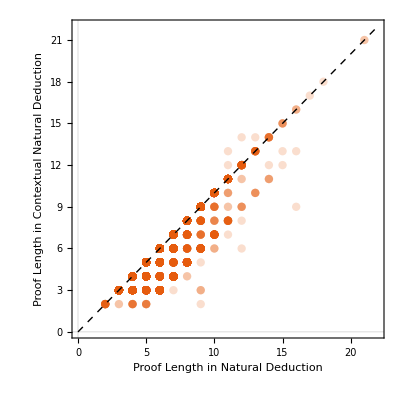

```mathematica
Show[ListPlot[lengths, PlotTheme->{"Scientific"},PlotStyle->{PointSize[0.015],Opacity[0.2]},Frame->True, PlotRange-> {{0,22},{0,22}},AspectRatio->Automatic],Plot[x,{x,0,22},PlotTheme->{"Monochrome"}, PlotStyle->{Thin,Dashed}],FrameLabel->{{HoldForm[Proof Length in Contextual Natural Deduction],None},{HoldForm[Proof Length in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/Scatter.pdf",%157,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/Scatter.pdf
 |  |  |  |

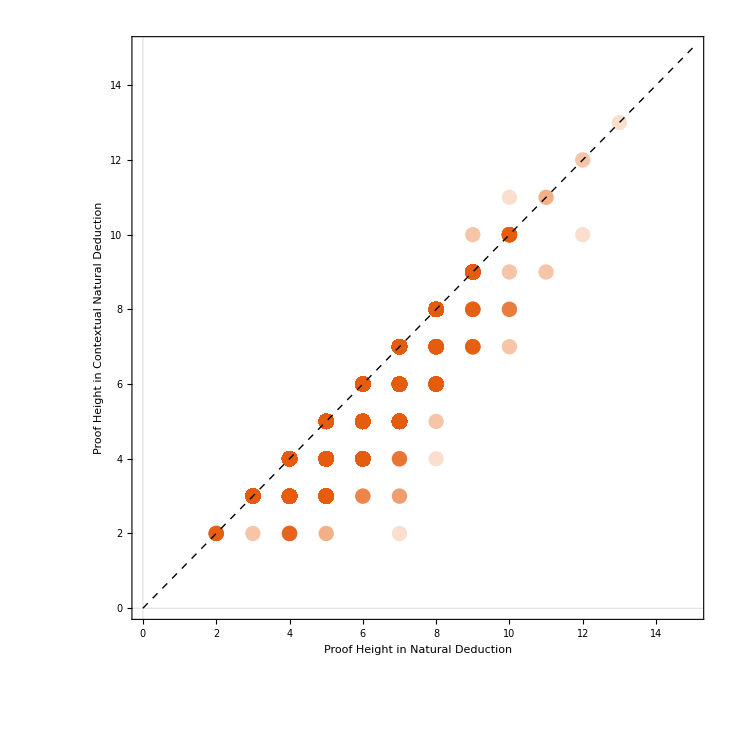

```mathematica
Show[ListPlot[heights, PlotTheme->{"Scientific"},PlotStyle->{PointSize[0.015],Opacity[0.2]},Frame->True, PlotRange-> {{0,15},{0,15}},AspectRatio->Automatic],Plot[x,{x,0,15},PlotTheme->{"Monochrome"}, PlotStyle->{Thin,Dashed}],FrameLabel->{{HoldForm[Proof Height in  Contextual Natural Deduction],None},{HoldForm[Proof Height in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

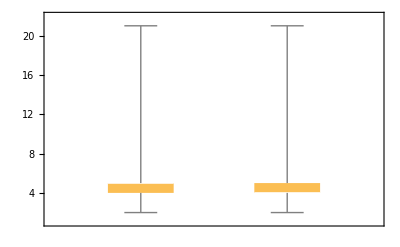

```mathematica
BoxWhiskerChart[Transpose[lengths]]
```

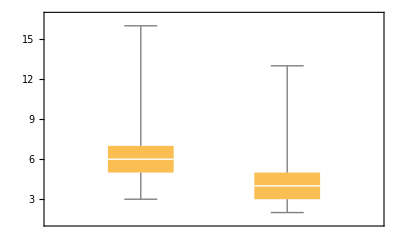

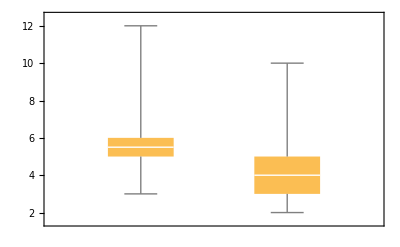

```mathematica
BoxWhiskerChart[filteredLengths]
BoxWhiskerChart[filteredHeights]
```

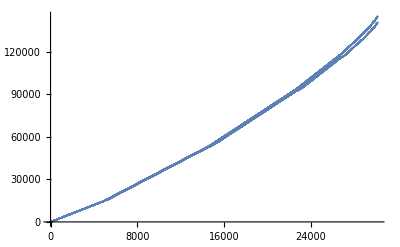

```mathematica
sorted = Sort[lengths,(#1[[1]] < #2[[1]] || (#1[[1]] == #2[[1]] && #1[[2]] < #2[[2]]))& ];
acummulated =Accumulate/@ Transpose[sorted];
Show[ListPlot[acummulated[[1]]],ListPlot[acummulated[[2]]]]
```

#### Grouping by Original Length

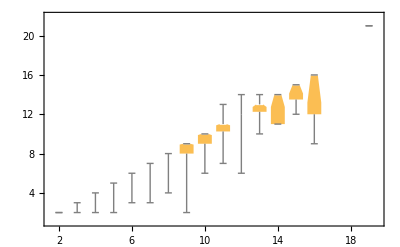

```mathematica
grouped = KeySort[GroupBy[lengths,#[[1]]&]];
g = grouped[[All,All,2]];BoxWhiskerChart[g,"Notched", ChartLabels-> Keys[g]]
```

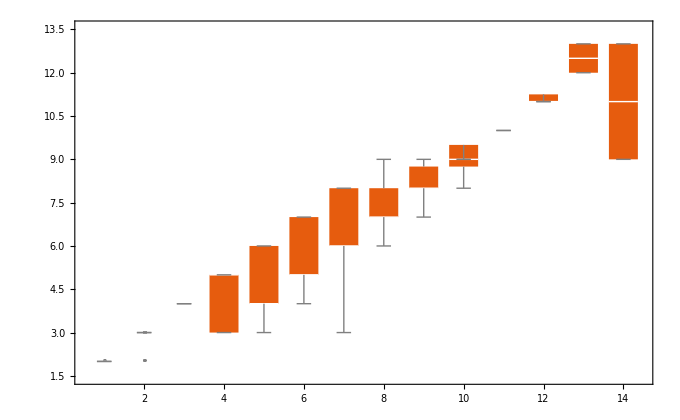

```mathematica
groupedFiltered = KeySort[GroupBy[Transpose[filteredLengths],#[[1]]&]];
gFiltered = groupedFiltered[[All,All,2]];
BoxWhiskerChart[gFiltered,"Outliers", ChartLabels-> Keys[gFiltered],FrameLabel->{{HoldForm[Proof Length in Contextual Natural Deduction],None},{HoldForm[Proof Length in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},PlotTheme->"Scientific"]
```

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/BoxWhiskers.pdf",%265,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/BoxWhiskers.pdf
 |  |  |  |

```mathematica
MapOverAssociation[f_,groupedData_] :=Association[(#[[1]] -> With[{t=Transpose[#[[2]]]}, f[t[[1]],t[[2]]]])& /@ Normal[groupedData]];
```

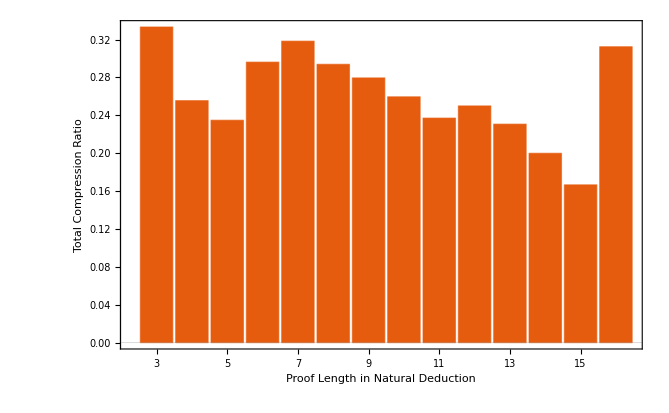

```mathematica
groupedTotalCompressionRatios= MapOverAssociation[TotalCompressionRatio,groupedFiltered];
BarChart[groupedTotalCompressionRatios,ChartLabels-> Keys[groupedTotalCompressionRatios],PlotTheme->"Scientific",FrameLabel->{{HoldForm[Total Compression Ratio],None},{HoldForm[Proof Length in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/CompressionByLength.pdf",%193,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/CompressionByLength.pdf
 |  |  |  |

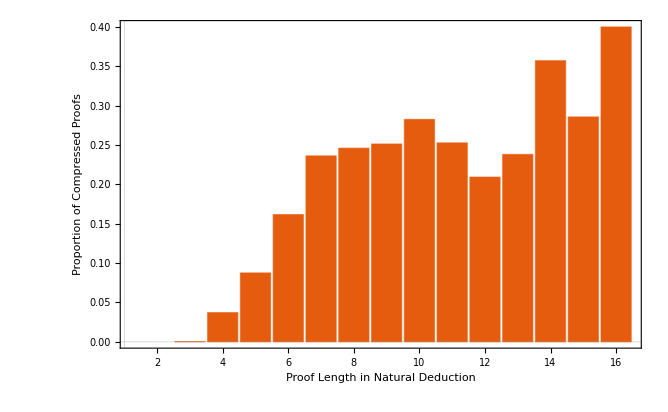

```mathematica
BarChart[groupedCompressionProportions,ChartLabels->Keys[groupedCompressionProportions],PlotTheme->"Scientific",FrameLabel->{{HoldForm[Proportion of Compressed Proofs],None},{HoldForm[Proof Length in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/Proportion by Length.pdf",%194,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/Proportion by Length.pdf
 |  |  |  |

#### 3D Plots Grouping by Original Length and Depth of Goal

```mathematica
data3D = select[data,where["NDLength"≠ -1  && "NDcLength"≠ -1],columns["GoalSize","GoalSymbols","GoalDepth","NDLength","NDcLength","NDTime","NDcTime"]];
data3DFiltered = select[data,where["NDLength"≠ -1  && "NDcLength"≠ -1 && "NDcLength" < "NDLength"],columns["GoalSize","GoalSymbols","GoalDepth","NDLength","NDcLength","NDTime","NDcTime"]];
```

```mathematica
groupedSizeSymbols = KeySort[GroupBy[data3D,{#[[1]],#[[2]]}&]]
groupedSizeDepth = KeySort[GroupBy[data3D,{#[[1]],#[[3]]}&]]
groupedFilteredSizeSymbols = KeySort[GroupBy[data3DFiltered,{#[[1]],#[[2]]}&]]
groupedFilteredSizeDepth = KeySort[GroupBy[data3DFiltered,{#[[1]],#[[3]]}&]]
```

<|{3,1}→{{3,1,3,3,3,28.3197,21.7494}},{4,1}→{{4,5,2.03705}},98,1,{15,14}→{{15,14,7,7,7,1.03562,38.0744},{15,14,8,7,7,0.97467,39.4701},{15,14,8,4,4,0.507931,1.11787},{15,14,6,5,5,0.782473,2.13035},{15,14,7,3,3,0.493869,0.69446},{15,14,8,4,4,0.543257,1.02048},286,{15,14,8,5,5,0.66002,2.18982},{15,14,8,6,6,0.838872,7.55376},{15,14,6,5,5,0.893507,2.18415},{15,14,9,6,6,1.0107,7.76546},{15,14,7,4,4,0.603184,1.00023},{15,14,9,5,5,0.78363,2.50577}}|>
 |  |  |  |

<|{3,3}→{{3,1,3,3,3,28.3197,21.7494}},{4,3}→{{4,1,3,2,2,0.723375,2.03705}},61,{15,12}→{{15,1,12,4,4,1.15308,1231.41},{15,8,12,7,7,1.04755,20.6814},{15,9,12,5,5,1.47996,606.934}}|>
 |  |  |  |

<|{4,2}→{{4,2,4,5,2,2.51107,11.4736}},{5,1}→{{5,1,5,4,3,0.841096,7.79947}},81,{15,13}→{{15,13,7,9,6,1.29945,397.948},{15,13,7,8,5,1.23327,62.7809},{15,13,7,8,5,1.17408,62.7085},{15,13,8,7,4,0.968677,11.2841}}|>
 |  |  |  |

<|{4,4}→{{4,2,4,5,2,2.51107,11.4736}},{5,5}→{{5,1,5,4,3,0.841096,7.79947}},49,{15,11}→{{15,1,11,5,4,1.22778,6484.15},{15,2,11,4,3,1.71143,474.309},{15,5,11,7,4,1.0253,13.001}}|>
 |  |  |  |

```mathematica
TotalCompressions[assoc_]:=  Function[d,With [{original = Transpose[d][[4]]},With[{compressed = Transpose[d][[5]]},TotalCompressionRatio[original,compressed]]]]/@ assoc;
gSizeSymbolsCompression = ListPlot3D[TotalCompressions[groupedSizeSymbols],PlotTheme->"Scientific",InterpolationOrder-> 1,ColorFunction->"SouthwestColors",Mesh->All,AxesLabel-> {"Formula Size","Distinct Atoms",Rotate["Compression Ratio",Pi/2]},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},BaseStyle->{FontWeight -> "Bold",FontSize->14}]
```

-Graphics3D-

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeSymbolsCompression.pdf",%297,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeSymbolsCompression.pdf
 |  |  |  |

```mathematica
ListPlot3D[TotalCompressions[groupedFilteredSizeSymbols],PlotTheme->"Scientific",InterpolationOrder-> 1,ColorFunction->"SouthwestColors",Mesh->All,AxesLabel-> {"Formula Size","Distinct Atoms",Rotate["Compression Ratio",Pi/2]},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},BaseStyle->{FontWeight -> "Bold",FontSize->14}]
```

-Graphics3D-

```mathematica
gSizeDepthCompression = ListPlot3D[TotalCompressions[groupedSizeDepth],PlotTheme->"Scientific",InterpolationOrder-> 1,ColorFunction->"SouthwestColors",Mesh->All,AxesLabel-> {"Formula Size","Formula Depth",Rotate["Compression Ratio",Pi/2]},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},BaseStyle->{FontWeight -> "Bold",FontSize->14}]
```

-Graphics3D-

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeDepthCompression.pdf",%250,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeDepthCompression.pdf
 |  |  |  |

```mathematica
ListPlot3D[TotalCompressions[groupedFilteredSizeDepth],PlotTheme->"Scientific",InterpolationOrder-> 1,ColorFunction->"SouthwestColors",Mesh->All,AxesLabel-> {"Formula Size","Formula Depth",Rotate["Compression Ratio",Pi/2]},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},BaseStyle->{FontWeight -> "Bold",FontSize->14}]
```

-Graphics3D-

```mathematica
Proportions[assoc_]:=  Function[d,Length[Select[d,#[[5]] < #[[4]]& ]]/Length[d]]/@ assoc
gSizeSymbolsProportion=ListPlot3D[Proportions[groupedSizeSymbols],PlotTheme->"Scientific",InterpolationOrder-> 1,ColorFunction->"SouthwestColors",Mesh->All,AxesLabel-> {"Size","Distinct Atoms",Rotate["",Pi/2]},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},BaseStyle->{FontWeight -> "Bold",FontSize->16}]
```

-Graphics3D-

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeSymbolsProportion.pdf",%234,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeSymbolsProportion.pdf
 |  |  |  |

```mathematica
gSizeDepthProportion=ListPlot3D[Proportions[groupedSizeDepth],PlotTheme->"Scientific",InterpolationOrder-> 1,ColorFunction->"SouthwestColors",Mesh->All,AxesLabel-> {"Size","Depth",Rotate["",Pi/2]},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},BaseStyle->{FontWeight -> "Bold",FontSize->16}]
```

-Graphics3D-

```mathematica
Export["/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeDepthProportion.pdf",%236,"PDF"]
```

/Users/Bruno/Dropbox/Pesquisa/Projects/Skeptik/Papers/ContextualNDEvaluation/Charts/3DSizeDepthProportion.pdf
 |  |  |  |

```mathematica
GraphicsGrid[{{gSizeSymbolsProportion,gSizeDepthProportion},{gSizeSymbolsCompression,gSizeDepthCompression}}]
```

-Graphics-

```mathematica
g = grouped[[All,All,2]];BoxWhiskerChart[g,"Notched", ChartLabels-> Keys[g]]
```

-Graphics-

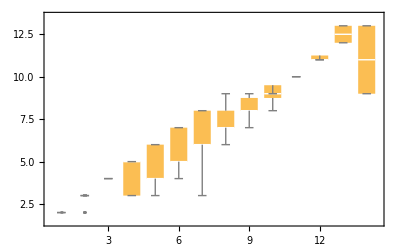

```mathematica
groupedFiltered = KeySort[GroupBy[Transpose[filteredLengths],#[[1]]&]];
gFiltered = groupedFiltered[[All,All,2]];
BoxWhiskerChart[gFiltered,"Outliers", ChartLabels-> Keys[gFiltered]]
```

```mathematica
MapOverAssociation[f_,groupedData_] :=Association[(#[[1]] -> With[{t=Transpose[#[[2]]]}, f[t[[1]],t[[2]]]])& /@ Normal[groupedData]];
```

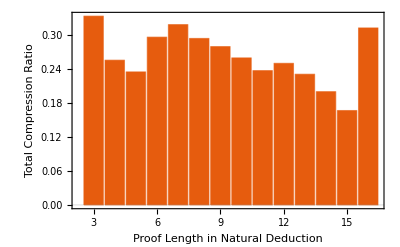

```mathematica
groupedTotalCompressionRatios= MapOverAssociation[TotalCompressionRatio,groupedFiltered];
BarChart[groupedTotalCompressionRatios,ChartLabels-> Keys[groupedTotalCompressionRatios],PlotTheme->"Scientific",FrameLabel->{{HoldForm[Total Compression Ratio],None},{HoldForm[Proof Length in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

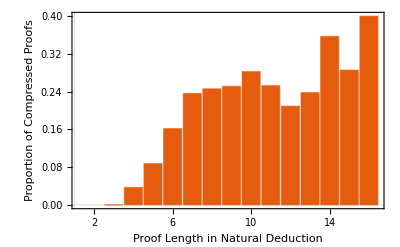

```mathematica
BarChart[groupedCompressionProportions,ChartLabels->Keys[groupedCompressionProportions],PlotTheme->"Scientific",FrameLabel->{{HoldForm[Proportion of Compressed Proofs],None},{HoldForm[Proof Length in Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

### Time

#### Basic Stats

```mathematica
times = select[data,where["NDLength"≠ -1  && "NDcLength"≠ -1],columns["NDTime","NDcTime"]];
timesTrans = Transpose[times];
Mean/@timesTrans
Median/@timesTrans
Quartiles/@timesTrans
```

{1.00943,9452.01}
 |  |  |  |

{0.946174,35.5414}
 |  |  |  |

{{0.581897,0.946174,1.34489},{2.40029,35.5414,521.9}}
 |  |  |  |

```mathematica
filteredTimes = select[data,where["NDLength"≠ -1  && "NDcLength"≠ -1 && "NDcLength" < "NDLength"],columns["NDTime","NDcTime"]];
filteredTimesTrans = Transpose[filteredTimes];
Mean/@filteredTimesTrans
Median/@filteredTimesTrans
Quartiles/@filteredTimesTrans
```

{1.2249,37572.6}
 |  |  |  |

{1.25558,1427.34}
 |  |  |  |

{{0.847741,1.25558,1.53403},{189.757,1427.34,13498.2}}
 |  |  |  |

```mathematica
allTimes = select[data,columns["NDTime","NDcTime"]];
allTimesTrans=Transpose[allTimes];
allTimesND = allTimesTrans[[1]];
```

```mathematica
valid = select[data,where["NDLength" ≠ -1]];
countersat = select[data, where["NDLength" == -1 && "NDTime" < 30000]];
timeout=select[data, where["NDLength" == -1 && "NDTime" >= 30000]];
numValid = Length[valid]
numCountersat = Length[countersat]
numTimeout = Length[timeout]
```

30127

46628

0

```mathematica
timeoutNDc = select[data, where["NDTime" < 30000 && "NDcTime" >= 300000]];
numNDcTimeout=Length[timeoutNDc]
```

533

```mathematica
Length[Select[allTimes,#[[1]]>#[[2]]&]]
Length[Select[allTimes,#[[2]]>#[[1]]&]]
```

```mathematica
46733/(76755)//N
```

0.608859

```mathematica
filteredTimes = select[data,where["NDLength" ≠ -1 &&"NDcLength" ≠ -1 && "NDLength" > "NDcLength"],columns["NDTime","NDcTime"]]
Length[Select[filteredTimes,#[[1]]>#[[2]]&]]
Length[Select[filteredTimes,#[[2]]>#[[1]]&]]
```

{{2.51107,11.4736},{0.841096,7.79947},{0.848883,47.8376},{0.869026,63.605},{0.587253,65.5624},{0.998599,74.9718},{0.292265,39.7776},{0.349353,35.3343},{0.315006,6.96355},{0.521228,52.245},{0.299913,33.3324},2535,{1.09596,20.415},{1.12692,52.883},{1.04646,20.7869},{1.07922,35.5598},{0.87107,4.97522},{2.04719,177.248},{0.784276,1.85708},{1.29945,397.948},{1.23327,62.7809},{1.17408,62.7085},{0.968677,11.2841}}
 |  |  |  |

0

2557

```mathematica
validTimes = select[data,where["NDLength" ≠ -1],columns["NDTime","NDcTime"]]
Length[Select[validTimes,#[[1]]>#[[2]]&]]
Length[Select[validTimes,#[[2]]>#[[1]]&]]
```

{{28.3197,21.7494},{0.723375,2.03705},{2.51107,11.4736},{0.841096,7.79947},{1.04796,3.86464},{0.657494,1.62122},{0.522295,4.52537},{1.13256,10.4937},{0.438064,5.04669},{0.479774,4.64137},{0.647968,5.04771},{0.802592,1.10646},30104,{0.644508,1.03403},{1.22381,37.9488},{0.638044,1.0763},{0.723058,2.61049},{0.937052,7.45157},{0.66002,2.18982},{0.838872,7.55376},{0.893507,2.18415},{1.0107,7.76546},{0.603184,1.00023},{0.78363,2.50577}}
 |  |  |  |

105

30022

#### Basic Plots

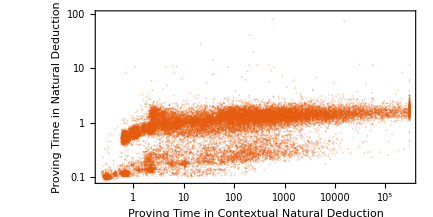

```mathematica
ListLogLogPlot[{#[[2]],#[[1]]}&/@times,PlotTheme->{"Scientific"},PlotRange-> {{0,300000},{0,100}},PlotStyle->{Opacity[0.33]},Frame->True,AspectRatio->Automatic,FrameLabel->{{HoldForm[Proving Time in Natural Deduction],None},{HoldForm[Proving Time in Contextual Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

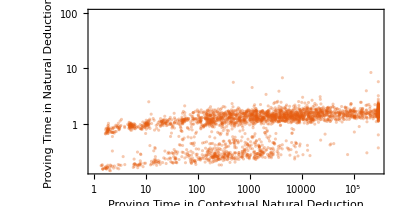

```mathematica
ListLogLogPlot[{#[[2]],#[[1]]}&/@filteredTimes,PlotTheme->{"Scientific"},PlotRange-> {{0,300000},{0,100}},PlotStyle->{Opacity[0.33]},Frame->True,AspectRatio->Automatic,FrameLabel->{{HoldForm[Proving Time in Natural Deduction],None},{HoldForm[Proving Time in Contextual Natural Deduction],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

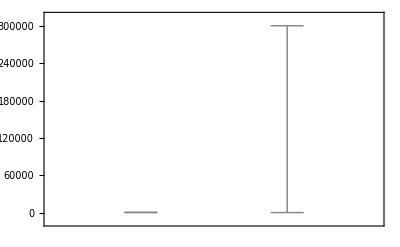

```mathematica
BoxWhiskerChart[timesTrans]
```